0.375

1.5

0.1875

0.09375

3.

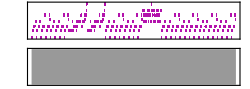

```mathematica
p4=60./80;

p8=p4/2
p2=2 p4
p16=p8/2
p32=p16/2
p=4 p4
music={{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p8},{"F",p8},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p8},{"F",p8},

{"C",1.5p8},{"C",p4},{"C",p8},{"C",p8},{"E4",p8},{"C",p8},
{"D",1.5p8},{"D",p4},{"D",p8},{"D",p16},{"C",p16},{"D",p16},{"E4",p16},{"D",p8},
{"E4",1.5p8},{"E4",p4},{"E4",p8},{"E4",p8},{"G",p8},{"D",p8},
{"E4",1.5p8},{"E4",p4},{"F4",p8},{"G4",p8},{"F4",p8},{"G4",p8},{"A4",p16},{"C5",p16},
{"C",1.5p8},{"C",p4},{"C",p8},{"C",p8},{"E4",p8},{"C",p8},
{"D",1.5p8},{"D",p4},{"D",p8},{"D",p16},{"C",p16},{"D",p16},{"E4",p16},{"D",p8},
{"E4",1.5p8},{"E4",p4},{"E4",p8},{"E4",p8},{"G",p8},{"D",p8},
{"E4",1.5p8},{"E4",p4},{"F4",p8},{"G4",p8},{"F4",p8},{"G4",p8},{"A4",p16},{"C5",p16},

{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p8},{"F",p8},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p8},{"F",p8},

{"A4",p8},{"G4",p8},{"E4",p8},{"A4",p8},{"G4",p8},{"E4",p4},{"G4",p8},
{"A4",p8},{"G4",p8},{"E4",p8},{"A4",p8},{"G4",p8},{"E4",p4},{"C5",p8},
{"A4",p8},{"G4",p8},{"E4",p8},{"A4",p8},{"G4",p8},{"E4",p4},{"G4",p8},
{"A4",p8},{"G4",p8},{"E4",p8},{"A4",p8},{"G4",p8},{"E4",p4},{"A4",p8},

{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p8},{"F",p8},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p8},{"F",p8},

{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p8},{"F",p8},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"E",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p4},
{"A3",p8},{"C4",p4},{"D4",1.5 p4},{"G",p8},{"F",p8}
};
Sound[{"Violin",Table[SoundNote[Part[music,i,1],Part[music,i,2]],{i,1,Length[music]}]}]
```